# SyntheticBenchmark

## Model Layer Distribution By Task

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=KeyDrop[SyntheticBenchmark`Assets`Models`$Models,"LeNet"];
```

```mathematica
models=Sort@GroupBy[Keys[$Models],If[NetModel[ #,"TaskType"]==={},"Other",First[NetModel[ #,"TaskType"]]]&];
```

```mathematica
figs=Table[
task=task0;
ms=Lookup[$Models,models[task]];
layers=Select[Counts[Flatten[ms][[All,0,1]]],#>Length[Flatten[ms]]/20&];
data=ReverseSort[layers];
BarChart[
data,
ChartLabels->Map[Rotate[Style[StringReplace[SymbolName[#],{"Layer"->"","Convolution"->"Conv","BatchNormalization"->"BN","Transpose"->"Tr","Elementwise"->"Elem","Normalization"->"Norm","Padding"->"Pad","Threading"->"Thrd","Catenate"->"Cat"}],FontSize->10,FontFamily->"Latin Modern Roman"],90Degree]&,Keys[data]],
ChartStyle->{Black},
PlotTheme->"Grid",
AspectRatio->1/4,
Frame->True,
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->8},
PlotLabel->task<>" Task"
],
{task0,Keys[models]}
];
```

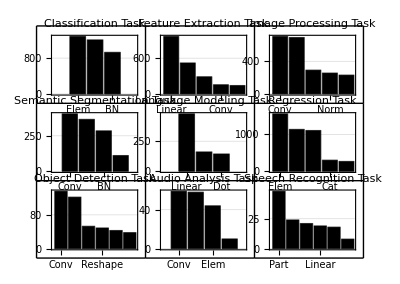

```mathematica
GraphicsGrid[Partition[figs,UpTo[3]],Frame->All,ImageMargins->0, ImageSize->Scaled[0.75]]
```

```mathematica
Import["http://tinyurl.com/ntmhkca"]
```

```mathematica
layers
```

<|ConvolutionLayer→1207,BatchNormalizationLayer→929,ElementwiseLayer→1284|>

```mathematica
tasks=Union[Flatten[Map[NetModel[ #,"TaskType"]&,Keys[$Models]]]]
```

{Audio Analysis,Classification,Feature Extraction,Image Processing,Language Modeling,Object Detection,Regression,Semantic Segmentation,Speech Recognition}

```mathematica
task="Object Detection";
ms=Lookup[$Models,models[task]];
layers=Select[Counts[Flatten[ms][[All,0,1]]],#>Length[Flatten[ms]]/20&];
ms=Association[Table[model->With[{info=Counts[Flatten[$Models[model]][[All,0,1]]]},Table[Lookup[info,layer,0],{layer,Keys[layers]}]],{model,models[task]}]];
```

```mathematica
Keys[models]
```

{Speech Recognition,Audio Analysis,Object Detection,Regression,Language Modeling,Semantic Segmentation,Image Processing,Feature Extraction,Classification}

```mathematica
Keys[layers]
```

{ElementwiseLayer,LinearLayer,DotLayer,ConvolutionLayer,BatchNormalizationLayer}

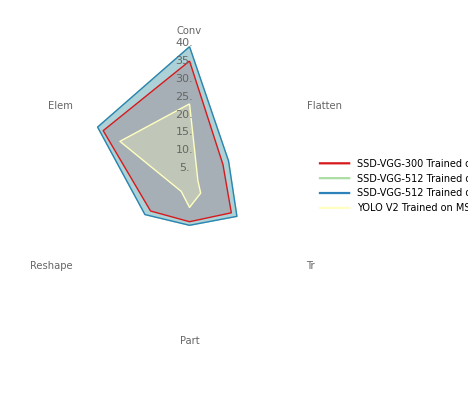

```mathematica
Needs["RadarChart`"]
RadarChart[Values[ms],Filling->Axis,AxesLabel->Map[Style[StringReplace[SymbolName[#],{"Layer"->"","Convolution"->"Conv","BatchNormalization"->"BN","Transpose"->"Tr","Elementwise"->"Elem","Normalization"->"Norm","Padding"->"Pad","Threading"->"Thrd","Catenate"->"Cat"}],FontSize->10,FontFamily->"Latin Modern Roman"]&,Keys[layers]],PlotStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[1., 1., 0.7490196078431373],GrayLevel[1]},ChartLegends->Keys[ms]]
```

## Model Layer Distribution

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=SyntheticBenchmark`Assets`Models`$Models;
```

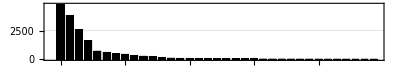

```mathematica
data=ReverseSort[Counts[Flatten[Values[$Models]][[All,0,1]]]];
BarChart[
data,
ChartLabels->Map[Rotate[Style[#,FontSize->10,FontFamily->"Latin Modern Roman"],90Degree]&,Keys[data]],
ChartStyle->{Black},
PlotTheme->"Grid",
AspectRatio->1/6,
Frame->True,
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
]
```

## Model Uniqueness

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=SyntheticBenchmark`Assets`Models`$Models;
```

```mathematica
unq=Association@KeyValueMap[
Function[{key,val},
key->{Length[val],Length[Union[val]],N[Length[Union[val]]/Length[val]]}
],
$Models
];
```

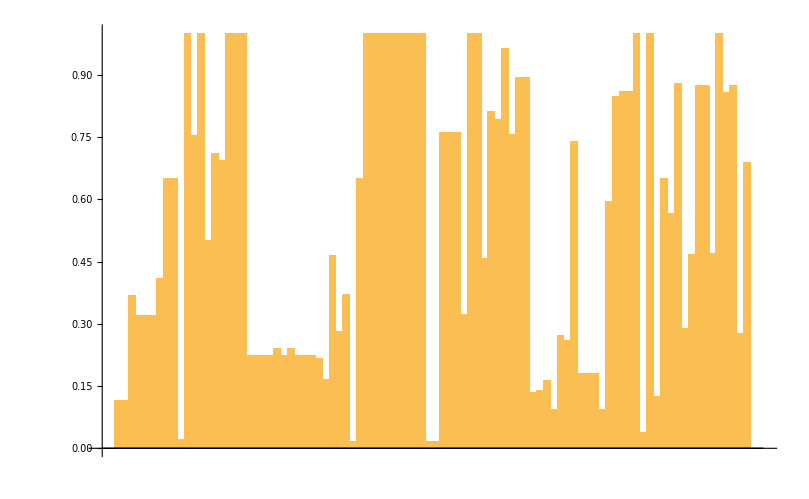

```mathematica
BarChart[MapThread[Tooltip,{Values[unq][[All,-1]],Keys[unq]}],PlotRange->All]
```

```mathematica
Grid[Normal[Select[unq,#[[-1]]<0.5&]]/.HoldPattern[Rule[x__]]:>Flatten[List[x]],Frame->All]
```

2D Face Alignment Net Trained on 300W Large Pose Data | 967 | 112 | 0.115822
3D Face Alignment Net Trained on 300W Large Pose Data | 967 | 112 | 0.115822
AdaIN-Style Trained on MS-COCO and Painter by Numbers Data | 109 | 40 | 0.366972
Ademxapp Model A1 Trained on ADE20K Data | 141 | 45 | 0.319149
Ademxapp Model A1 Trained on Cityscapes Data | 141 | 45 | 0.319149
Ademxapp Model A1 Trained on PASCAL VOC2012 and MS-COCO Data | 141 | 45 | 0.319149
Ademxapp Model A Trained on ImageNet Competition Data | 142 | 58 | 0.408451
BERT Trained on BookCorpus and English Wikipedia Data | 862 | 19 | 0.0220418
CycleGAN Apple-to-Orange Translation Trained on ImageNet Competition Data | 94 | 21 | 0.223404
CycleGAN Horse-to-Zebra Translation Trained on ImageNet Competition Data | 94 | 21 | 0.223404
CycleGAN Monet-to-Photo Translation | 94 | 21 | 0.223404
CycleGAN Orange-to-Apple Translation Trained on ImageNet Competition Data | 94 | 21 | 0.223404
CycleGAN Photo-to-Cezanne Translation | 96 | 23 | 0.239583
CycleGAN Photo-to-Monet Translation | 94 | 21 | 0.223404
CycleGAN Photo-to-Van Gogh Translation | 96 | 23 | 0.239583
CycleGAN Summer-to-Winter Translation | 94 | 21 | 0.223404
CycleGAN Winter-to-Summer Translation | 94 | 21 | 0.223404
CycleGAN Zebra-to-Horse Translation Trained on ImageNet Competition Data | 94 | 21 | 0.223404
Deep Speech 2 Trained on Baidu English Data | 152 | 33 | 0.217105
Dilated ResNet-105 Trained on Cityscapes Data | 360 | 60 | 0.166667
Dilated ResNet-22 Trained on Cityscapes Data | 86 | 40 | 0.465116
Dilated ResNet-38 Trained on Cityscapes Data | 142 | 40 | 0.28169
ELMo Contextual Word Representations Trained on 1B Word Benchmark | 111 | 41 | 0.369369
Enhanced Super-Resolution GAN Trained on DIV2K, Flickr2K and OST Data | 1093 | 17 | 0.0155535
GPT-2 Transformer Trained on WebText Data | 832 | 14 | 0.0168269
GPT Transformer Trained on BookCorpus Data | 857 | 15 | 0.0175029
Inception V3 Trained on ImageNet Competition Data | 311 | 100 | 0.321543
MobileNet V2 Trained on ImageNet Competition Data | 153 | 70 | 0.457516
ResNet-101 Trained on Augmented CASIA-WebFace Data | 345 | 46 | 0.133333
ResNet-101 Trained on ImageNet Competition Data | 347 | 48 | 0.138329
ResNet-101 Trained on YFCC100m Geotagged Data | 344 | 56 | 0.162791
ResNet-152 Trained on ImageNet Competition Data | 517 | 48 | 0.0928433
ResNet-50 Trained on ImageNet Competition Data | 177 | 48 | 0.271186
Self-Normalizing Net for Numeric Data | 23 | 6 | 0.26087
Single-Image Depth Perception Net Trained on Depth in the Wild Data | 501 | 90 | 0.179641
Single-Image Depth Perception Net Trained on NYU Depth V2 and Depth in the Wild Data | 501 | 90 | 0.179641
Single-Image Depth Perception Net Trained on NYU Depth V2 Data | 501 | 90 | 0.179641
Squeeze-and-Excitation Net Trained on ImageNet Competition Data | 874 | 82 | 0.0938215
Unguided Volumetric Regression Net for 3D Face Reconstruction | 1029 | 40 | 0.0388727
Very Deep Net for Super-Resolution | 40 | 5 | 0.125
Wide ResNet-50-2 Trained on ImageNet Competition Data | 176 | 51 | 0.289773
Wolfram AudioIdentify V1 Trained on AudioSet Data | 156 | 73 | 0.467949
Wolfram ImageIdentify Net V1 | 232 | 109 | 0.469828
Yahoo Open NSFW Model V1 | 177 | 49 | 0.276836

```mathematica
Length[Union[$Models["MobileNet V2 Trained on ImageNet Competition Data"]]]/N@Length[$Models["MobileNet V2 Trained on ImageNet Competition Data"]]
```

0.457516

## Model Cache

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"SyntheticBenchmark","Assets","ModelsCache.mx"}]]
```

```mathematica
$Models=SyntheticBenchmark`Assets`Models`$Models;
```

## Generate Models MX File

```mathematica
Exit
```

```mathematica
PrependTo[$Path,NotebookDirectory[]];
```

```mathematica
<<SyntheticBenchmark`
<<SyntheticBenchmark`Assets`Models`
```

```mathematica
DumpSaveModelWeights[]
```